# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"../package/"];
Get["funcs_rxns_moms.m"]
```

# Setup data description

## Data description

```mathematica
nv=2;
nh=1;

noSeeds=1200;
tptStart=100;
tptMax=500;
tptInterval=1;
dt=0.1;
volExp=14;
noIP3R=100;

dataDesc=makeDataDesc[noSeeds,volExp,tptStart,tptMax,tptInterval,dt];
noTpts=dataDesc["noTpts"];
times=dataDesc["times"];
```

```mathematica
cdir=getCacheDir[dataDesc,noIP3R];
exportDataDesc[dataDesc,cdir<>"data_desc.txt"]
```

## Setup latent space

```mathematica
muhs={};
varhs={};
Do[
AppendTo[muhs,{0}//N];
AppendTo[varhs,{{1}}//N];
,{tpt,tptStart,tptMax,tptInterval}];
```

# Import and export to cache

## Functions

```mathematica
getDir[noIP3R_,ip3_,dataDesc_]:=Module[
{}
,
If[noIP3R<1000,
Return[NotebookDirectory[]<>"../../stochastic_simulations/ml_training_data/data_gillespie/vol_exp_"<>ToString[dataDesc["volExp"]]<>"/ip3r_"<>IntegerString[noIP3R,10,5]<>"/"<>ip3<>"/"],
Return[NotebookDirectory[]<>"../../stochastic_simulations/ml_training_data/data_tau_leaping/vol_exp_"<>ToString[dataDesc["volExp"]]<>"/ip3r_"<>IntegerString[noIP3R,10,5]<>"/"<>ip3<>"/"]
];
Return[NotebookDirectory[]];
]
```

```mathematica
importAndWhitenAndCalcParams[nv_,nh_,ip3_,noIP3R_,dataDesc_,muhs_,varhs_,mv_,sv_]:=Module[
{data,d1,d2,dims,mvArr,svArr,dataS,params,paramsLD,tpt,nd}
,
SetDirectory[getDir[noIP3R,ip3,dataDesc]];
data=importData[dataDesc,noIP3R]//N;
data=data[[(dataDesc["tptStart"]+1);;(dataDesc["tptMax"]+1);;dataDesc["tptInterval"]]];

dims=Dimensions[data][[;;2]];
mvArr=ConstantArray[mv,dims];
svArr=ConstantArray[sv,dims];

dataS=(data-mvArr)/svArr;

paramsLD={};
Do[
AppendTo[paramsLD,getMLparams[dataS[[i]],muhs[[i]],varhs[[i]]]];
,{i,dataDesc["noTpts"]}];

params=makePStructFromLD[nv,nh,paramsLD];

Return[params]
]
```

```mathematica
exportToCache[nv_,nh_,params_,dataDesc_,ip3_,noIP3R_]:=Module[
{cdir,x,fname}
,
cdir=getCacheDir[dataDesc,noIP3R]<>"params0/";
SetDirectory[NotebookDirectory[]];

If[!DirectoryQ[cdir<>ip3],CreateDirectory[cdir<>ip3]];
Do[
x=params["LFDL"][k];
fname=cdir<>ip3<>"/"<>k<>".txt";
Export[fname,StringRiffle[ToString[#,FortranForm]&/@PaddedForm[#,16]&/@x,"\n"]]
,{k,makeLF[nv,nh]}];
]
```

## Run

```mathematica
ip3s={
"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000",
"ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"
};

mv={0,0};
sv={1,1};

Monitor[
Do[
ip3=ip3s[[idx]];
params=importAndWhitenAndCalcParams[nv,nh,ip3,noIP3R,dataDesc,muhs,varhs,mv,sv];
exportToCache[nv,nh,params,dataDesc,ip3,noIP3R];
,{idx,Length[ip3s]}];
,Row[{"IP3: ",ProgressIndicator[idx,{1,Length[ip3s]}]}]]
```

# Re import and viz

## Import cache

```mathematica
nv=2;
nh=1;

volExp=14;
cdir=getCacheDirRaw[volExp,noIP3R];
SetDirectory[NotebookDirectory[]];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

```mathematica
SetDirectory[NotebookDirectory[]];

params0=Association[];
Do[

cdir=getCacheDirRaw[volExp,noIP3R];
pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"params0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

params0[ip3]=makePStructFromLFDL[nv,nh,pLFDL];
,{ip3,ip3s}];
```

## Viz

```mathematica
pltEvery=20;
timesPlt=dataDesc["times"][[;;;;pltEvery]];
colors=Table[ColorData["BrownCyanTones"][i/Length[ip3s]],{i,Length[ip3s]}]
```

{RGBColor[0.4328202, 0.2875746, 0.16778140000000002],RGBColor[0.5179634, 0.3752862, 0.2504938],RGBColor[0.5943548, 0.45806840000000004, 0.33588],RGBColor[0.6619944, 0.5359212, 0.42394],RGBColor[0.729634, 0.613774, 0.512],RGBColor[0.7668376, 0.6736248, 0.5867076],RGBColor[0.8040412, 0.7334756, 0.6614152],RGBColor[0.8253242000000001, 0.787301, 0.7308212],RGBColor[0.8306866, 0.835101, 0.7949256],RGBColor[0.836049, 0.882901, 0.85903],RGBColor[0.8065450000000001, 0.9053942, 0.8961547999999999],RGBColor[0.777041, 0.9278874, 0.9332796],RGBColor[0.7376514, 0.9364448, 0.9557662],RGBColor[0.6883762, 0.9310664, 0.9636146],RGBColor[0.639101, 0.925688, 0.971463],RGBColor[0.585357, 0.8967528, 0.9580974],RGBColor[0.531613, 0.8678176000000001, 0.9447318],RGBColor[0.4723912, 0.8128028, 0.9049796],RGBColor[0.40769160000000004, 0.7317084, 0.8388408],RGBColor[0.342992, 0.650614, 0.772702]}

```mathematica
lfPlt=Select[makeLF[nv,nh],StringLength[#]<4||(StringTake[#,4]!="varh"&&StringTake[#,3]!="muh")&]
```

{wt11,wt12,sig2,b1,b2}

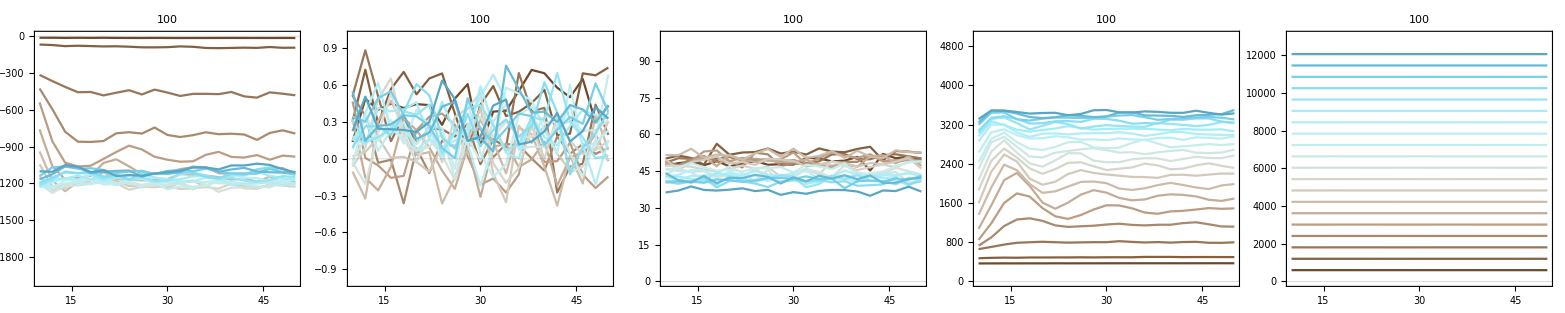

```mathematica
rngs=<|
"wt11"->{-2000,0},
"wt12"->{-1,1},
"sig2"->{0,100},
"b1"->{0,5000},
"b2"->{0,13000}
|>;

plts=Table[
Show[
Table[
ip3=ip3s[[i]];
xPlt=params0[ip3]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->labels[k],PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->rngs[k],
PlotLabel->ToString[noIP3R]<>" "<>labels[k],
FrameLabel->{"Time (s)"}
]
,{k,lfPlt}];

Grid[{plts}]
```